```mathematica
x1=-2.00;
x2=-3.00;
x3=1;
a0=1;
a1=0;
a2=1;
a3=0;
A=Table[0,{x,4},{y,4}];
A[[1,1]]=-2*a0*x3;
A[[1,2]]=0;
A[[1,3]]=a0*x1+a1*x3;
A[[1,4]]=a0*x2-a2*x3;
A[[2,1]]=0;
A[[2,2]]=-2*a0*x3;
A[[2,3]]=a0*x2+a2*x3;
A[[2,4]]=-a0*x1+a1*x3;
A[[3,1]]=a0*x1+a1*x3;
A[[3,2]]=a0*x2+a2*x3;
A[[3,3]]=-a1*x1-a2*x2+1/(2*x3)*(a3*x3^2-a0*x1^2-a0*x2^2);
A[[3,4]]=a2*x1-a1*x2;
A[[4,1]]=a0*x2-a2*x3;
A[[4,2]]=-a0*x1+a1*x3;
A[[4,3]]=a2*x1-a1*x2;
A[[4,4]]=a1*x1+a2*x2+1/(2*x3)*(a3*x3^2-a0*x1^2-a0*x2^2);
A
```

{{-2,0,-2.,-4.},{0,-2,-2.,2.},{-2.,-2.,-3.5,-2.},{-4.,2.,-2.,-9.5}}

```mathematica
q1=-2*a0*x3
q2=2*a0*x1
q3=2*a0*x2
q4=2*a1*x3
q5=2*a2*x3
q6=2*(a2*x1-a1*x2)
q7=-(a1*x1+a2*x2)
q8=1/(2*x3)*(a3*x3^2-a0*x1^2-a0*x2^2)
```

-2

-4.

-6.

0

2

-4.

3.

-6.5

```mathematica
x1=1;
x2=-3;
x3=1;
a0=0;
a1=1;
a2=2;
a3=2;
B=Table[0,{x,4},{y,4}];
B[[1,1]]=-2*a0*x3;
B[[1,2]]=0;
B[[1,3]]=a0*x1+a1*x3;
B[[1,4]]=a0*x2-a2*x3;
B[[2,1]]=0;
B[[2,2]]=-2*a0*x3;
B[[2,3]]=a0*x2+a2*x3;
B[[2,4]]=-a0*x1+a1*x3;
B[[3,1]]=a0*x1+a1*x3;
B[[3,2]]=a0*x2+a2*x3;
B[[3,3]]=-a1*x1-a2*x2+1/(2*x3)*(a3*x3^2-a0*x1^2-a0*x2^2);
B[[3,4]]=a2*x1-a1*x2;
B[[4,1]]=a0*x2-a2*x3;
B[[4,2]]=-a0*x1+a1*x3;
B[[4,3]]=a2*x1-a1*x2;
B[[4,4]]=a1*x1+a2*x2+1/(2*x3)*(a3*x3^2-a0*x1^2-a0*x2^2);
B
```

{{0,0,1,-2},{0,0,2,1},{1,2,6,5},{-2,1,5,-4}}

```mathematica
q1=-2*a0*x3
q2=2*a0*x1
q3=2*a0*x2
q4=2*a1*x3
q5=2*a2*x3
q6=2*(a2*x1-a1*x2)
q7=-(a1*x1+a2*x2)
q8=1/(2*x3)*(a3*x3^2-a0*x1^2-a0*x2^2)
```

0

0

0

2

4

10

5

1

```mathematica
myplot=ContourPlot3D[{A[[1, 1]]*x^2 + (A[[1, 2]] + A[[2, 1]])*x*y + (A[[1, 3]] + A[[3, 1]])*x*z + (A[[1, 4]] + A[[4, 1]])*x + A[[2, 2]]*y^2 + (A[[2, 3]] + A[[3, 2]])*y*z + (A[[2, 4]] + A[[4, 2]])*y + A[[3, 3]]*z^2 + (A[[3, 4]] + A[[4, 3]])*z + A[[4, 4]] == 0, B[[1, 1]]*x^2 + (B[[1, 2]] + B[[2, 1]])*x*y + (B[[1, 3]] + B[[3, 1]])*x*z + (B[[1, 4]] + B[[4, 1]])*x + B[[2, 2]]*y^2 + (B[[2, 3]] + B[[3, 2]])*y*z + (B[[2, 4]] + B[[4, 2]])*y + B[[3, 3]]*z^2 + (B[[3, 4]] + B[[4, 3]])*z + B[[4, 4]] == 0}, {x, -10, 10}, {y, -10, 10}, {z, -10, 10}, PerformanceGoal -> "Quality", MeshStyle -> Gray, Mesh -> 2, Boxed -> False, Axes -> True, AxesLabel -> {X, Y, Z}, MaxRecursion -> 15, PlotPoints -> 50, PlotRange -> Automatic, ContourStyle -> {{Orange, Opacity[0.5]}, {Magenta,Opacity[0.5]}}];
Show[myplot]
```

-Graphics3D-

```mathematica
eigenvalues=Eigenvalues[A];
eigenvectors=Eigenvectors[A];
transformatrix=Transpose[{eigenvectors[[3]],eigenvectors[[4]],eigenvectors[[1]], eigenvectors[[2]]}];
```

```mathematica
afterA=Transpose[transformatrix].A.transformatrix;
MatrixForm[afterA]
```

(0.19643 | 3.01842×10^-16 | -1.20043×10^-15 | 4.19803×10^-16
2.77556×10^-16 | 0.0820506 | -6.245×10^-17 | -1.33313×10^-15
-1.11022×10^-15 | -8.88178×10^-16 | -12.1876 | -3.55271×10^-15
3.60822×10^-16 | -1.27676×10^-15 | -3.55271×10^-15 | -5.09088)

```mathematica
afterB=Transpose[transformatrix].B.transformatrix;
MatrixForm[afterB]
```

(-0.979681 | -0.938678 | 3.64101 | 0.837837
-0.938678 | 1.43582 | -1.17606 | -1.75265
3.64101 | -1.17606 | -1.82257 | 5.73298
0.837837 | -1.75265 | 5.73298 | 3.36643)

```mathematica
Clear[V];Clear[u];Clear[v];
V={(u+afterA[[1,1]]*v)/afterA[[1,1]], (u*v-afterA[[2,2]])/afterA[[2,2]], (u-afterA[[1,1]]*v)/Sqrt[-afterA[[1,1]]*afterA[[3,3]]], (u*v+afterA[[2,2]])/Sqrt[-afterA[[2,2]]*afterA[[4,4]]]};
```

```mathematica
goalformula=Collect[Expand[V.afterB.V], {u^2, u}]
```

1.93508+1.60668 v-1.93353 v^2+u (13.1014-43.3516 v-18.9007 v^2)+u^2 (-2.192-110.344 v+155.231 v^2)

```mathematica
delta=Expand[(13.10136898336389-43.35157640379816 v-18.900674233234533 v^2)^2-4*(-2.192002848367311-110.34410242259166 v+155.23131437230128 v^2)*(1.9350841748486531+1.6066790409726013 v-1.9335335822795943 v^2)];
```

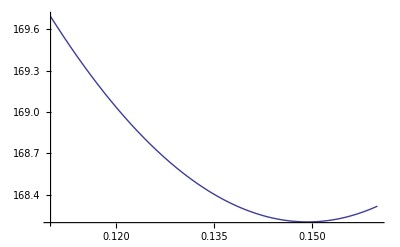

```mathematica
Plot[delta, {v,0.11, 0.16}]
```

```mathematica
Solve[delta==0, v]
```

{{v→-0.184881-0.691476 ⅈ},{v→-0.184881+0.691476 ⅈ},{v→0.25302-0.415099 ⅈ},{v→0.25302+0.415099 ⅈ}}

```mathematica
u1=(-(13.10136898336389-43.35157640379816 v-18.900674233234533 v^2)+Sqrt[delta])/(2*(-2.192002848367311-110.34410242259166 v+155.23131437230128 v^2));
u2=(-(13.10136898336389-43.35157640379816 v-18.900674233234533 v^2)-Sqrt[delta])/(2*(-2.192002848367311-110.34410242259166 v+155.23131437230128 v^2));
```

```mathematica
afterP1={(u1+afterA[[1,1]]*v)/afterA[[1,1]], (u1*v-afterA[[2,2]])/afterA[[2,2]], (u1-afterA[[1,1]]*v)/Sqrt[-afterA[[1,1]]*afterA[[3,3]]], (u1*v+afterA[[2,2]])/Sqrt[-afterA[[2,2]]*afterA[[4,4]]]};
afterP2={(u2+afterA[[1,1]]*v)/afterA[[1,1]], (u2*v-afterA[[2,2]])/afterA[[2,2]], (u2-afterA[[1,1]]*v)/Sqrt[-afterA[[1,1]]*afterA[[3,3]]], (u2*v+afterA[[2,2]])/Sqrt[-afterA[[2,2]]*afterA[[4,4]]]};
```

```mathematica
P1=transformatrix.afterP1;
P2=transformatrix.afterP2;
```

```mathematica
Branch1=Graphics3D[{PointSize[0.01],Black,Point[Table[{P1[[1]]/P1[[4]],P1[[2]]/P1[[4]],P1[[3]]/P1[[4]]},{v,-5, 5, 0.005}]]}, Axes -> True, AxesLabel -> {X, Y, Z},Boxed -> False];
Branch2=Graphics3D[{PointSize[0.01],Black,Point[Table[{P2[[1]]/P2[[4]],P2[[2]]/P2[[4]],P2[[3]]/P2[[4]]},{v, 0.022,1.2, 0.001}]]}];
Show[Branch1, Branch2,myplot]
```

-Graphics3D-